```mathematica
emptyTerms = {1->NonTerm["cond",3],2->Term["numOp"],3->NonTerm["numQuant",4],4->NonTerm["numQuant",5],5->NonTerm["expression",6],6->Term["techInd"],7->Term["observable"],8->Term["window"],9->Term["factor"],10->NonTerm["expression",6],11->Term["techInd"],12->Term["observable"],13->Term["window"]};
```

```mathematica
terminalSet
```

{Term[logicOp,And],Term[logicOp,Or],Term[logicOp,Xor],Term[numOp,Greater],Term[numOp,GreaterEqual],Term[numOp,Less],Term[numOp,LessEqual],Term[observable,Open],Term[observable,Low],Term[observable,High],Term[observable,Close],Term[lag,1],Term[lag,2],Term[lag,3],Term[lag,4],Term[lag,5],Term[window,10],Term[window,20],Term[window,30],Term[window,40],Term[window,50],Term[factor,0.7],Term[factor,0.9],Term[factor,1.1],Term[factor,1.3]}

```mathematica
ReplaceAll[emptyTerms,HoldPattern[v_->Term[n_]]:>(v->RandomTerm[n,terminalSet])]
```

{1→NonTerm[cond,3],2→Term[numOp,LessEqual],3→NonTerm[numQuant,4],4→NonTerm[numQuant,5],5→NonTerm[expression,6],6→Term[techInd,SMA],7→Term[observable,High],8→Term[window,30],9→Term[factor,1.1],10→NonTerm[expression,6],11→Term[techInd,SMA],12→Term[observable,High],13→Term[window,40]}

```mathematica
Cases[emptyTerms,HoldPattern[_->Term[_]]]
```

{2→Term[numOp],6→Term[techInd],7→Term[observable],8→Term[window],9→Term[factor],11→Term[techInd],12→Term[observable],13→Term[window]}

```mathematica
RandomTerm[name_,terminalSet_]:=RandomChoice[Cases[terminalSet,Term[name,_]]];
```

```mathematica
RandomTerm["techInd",terminalSet]
```

Term[techInd,EMA]

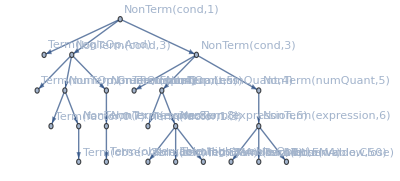
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,GreaterEqual],6→NonTerm[numQuant,4],7→NonTerm[numQuant,5],8→Term[numOp,Less],9→NonTerm[numQuant,4],10→NonTerm[numQuant,5],11→Term[factor,1.3],12→NonTerm[expression,6],13→NonTerm[expression,8],14→Term[techInd,EMA],15→Term[observable,Open],16→Term[window,10],17→Term[factor,0.7],18→NonTerm[expression,8],19→Term[observable,Low],20→NonTerm[expression,6],21→Term[observable,High],22→Term[techInd,EMA],23→Term[observable,Close],24→Term[window,50]}}

```mathematica
{g,l} = GenerateRandomFunction[grammar,terminalSet]
```

```mathematica
SynthesizeTree[g,l,grammar] // FullForm
```

And[GreaterEqual[Times[0.7,Low],High],Less[Times[1.3,EMA[Open,10]],EMA[Close,50]]]